```mathematica
f[x_]:=(1-(x^2-xmu2)/((x x-xmu2)^2+xdt2)^(1/2))x x
```

```mathematica
f[x]
```

x^2 (1-(x^2-xmu2)/(√(xdt2+(x^2-xmu2)^2)))

```mathematica
NIntegrate[f[x]/.{xmu2->1,xdt2->0.0001},{x,0,Infinity}]
```

0.666846

```mathematica
N[%]
```

0.666846

```mathematica
NSolve[NIntegrate[(f[x]/.{xmu2->0.9}),{x,0,Infinity}]==2/3,{xdt2},Reals]
```

NIntegrate::inumr: The integrand x^2\ (1 - -0.9 + x^2/√(-0.9 + Power[« 2 »])^2 + xdt2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{}

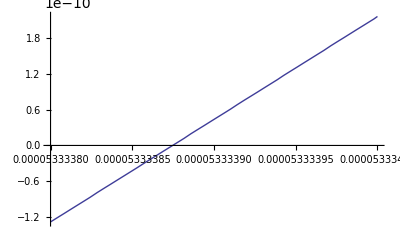

```mathematica
Plot[NIntegrate[(f[x]/.{xmu2->0.9999}),{x,0,Infinity}]-2/3,{xdt2,0.0000533338,0.000053334}]
```

```mathematica
N[8Pi^3/3]
```

82.6834

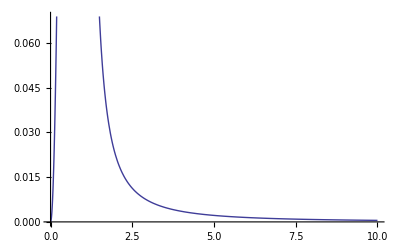

```mathematica
Plot[f[x]/.{xmu2->0.99,xdt2->0.1},{x,0,10}]
```

```mathematica
muDtL={{0.9999,0.00005333385},{0.999,0.00064},{0.99,0.0079665},{0.97,0.0269707},{0.95,0.0476463},{0.94,0.05837507},{0.93,0.0693001},{0.9,0.10298},{0.8,0.2205},{0.7,0.34},{0.6,0.46005},{0.5,.577},{.3,.8005},{.1,1.01},{0,1.107},{-0.1,1.2},{-0.3,1.38},{-.5,1.545},{-.7,1.7},{-.9,1.854},{-1,1.915},{-1.5,2.24},{-2,2.525},{-2.5,2.785},{-3,3.02},{-4,3.46},{-5,3.85},{-6,4.2},{-8,4.85},{-10,5.4}}
```

{{0.9999,0.0000533339},{0.999,0.00064},{0.99,0.0079665},{0.97,0.0269707},{0.95,0.0476463},{0.94,0.0583751},{0.93,0.0693001},{0.9,0.10298},{0.8,0.2205},{0.7,0.34},{0.6,0.46005},{0.5,0.577},{0.3,0.8005},{0.1,1.01},{0,1.107},{-0.1,1.2},{-0.3,1.38},{-0.5,1.545},{-0.7,1.7},{-0.9,1.854},{-1,1.915},{-1.5,2.24},{-2,2.525},{-2.5,2.785},{-3,3.02},{-4,3.46},{-5,3.85},{-6,4.2},{-8,4.85},{-10,5.4}}

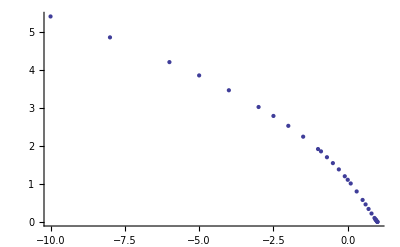

```mathematica
ListPlot[muDtL]
```

```mathematica
f1[x_]:=(x x)/((x x-xmu2)^2+xdt4)^(1/2)-1
```

```mathematica
f1[x]
```

-1+x^2/(√(xdt4+(x^2-xmu2)^2))

```mathematica
f1[x]mu{xmu2->1,xdt4->2}
```

{mu (-1+x^2/(√(xdt4+(x^2-xmu2)^2))) (xmu2→1),mu (-1+x^2/(√(xdt4+(x^2-xmu2)^2))) (xdt4→2)}

```mathematica
length=Length[muDtL];intact={};
For[i=1,i≤length,i++,
strength=2/Pi NIntegrate[f1[x]/.{xmu2->muDtL[[i,1]],xdt4->muDtL[[i,2]]},{x,0,Infinity}];intact=Append[intact,strength]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99228}. NIntegrate obtained 4.99858 and 0.0000122024 for the integral and error estimates.

```mathematica
intact
```

{3.1822,2.38973,1.5756,1.16658,0.967024,0.893712,0.830707,0.680721,0.367452,0.166638,0.0128024,-0.113235,-0.316811,-0.481182,-0.553235,-0.620286,-0.742788,-0.852479,-0.952547,-1.04524,-1.08865,-1.28824,-1.46346,-1.6213,-1.76587,-2.02578,-2.25686,-2.46689,-2.84159,-3.17282}

```mathematica
muL=Transpose[muDtL][[1]];dtL=Transpose[muDtL][[2]]^(1/2);
```

```mathematica
muL
```

{0.9999,0.999,0.99,0.97,0.95,0.94,0.93,0.9,0.8,0.7,0.6,0.5,0.3,0.1,0,-0.1,-0.3,-0.5,-0.7,-0.9,-1,-1.5,-2,-2.5,-3,-4,-5,-6,-8,-10}

```mathematica
Transpose[{intact,muL}]
```

{{3.1822,0.9999},{2.38973,0.999},{1.5756,0.99},{1.16658,0.97},{0.967024,0.95},{0.893712,0.94},{0.830707,0.93},{0.680721,0.9},{0.367452,0.8},{0.166638,0.7},{0.0128024,0.6},{-0.113235,0.5},{-0.316811,0.3},{-0.481182,0.1},{-0.553235,0},{-0.620286,-0.1},{-0.742788,-0.3},{-0.852479,-0.5},{-0.952547,-0.7},{-1.04524,-0.9},{-1.08865,-1},{-1.28824,-1.5},{-1.46346,-2},{-1.6213,-2.5},{-1.76587,-3},{-2.02578,-4},{-2.25686,-5},{-2.46689,-6},{-2.84159,-8},{-3.17282,-10}}

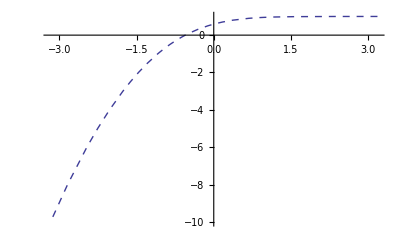

```mathematica
muPlot=ListLinePlot[Transpose[{intact, muL}],PlotStyle->Dashed]
```

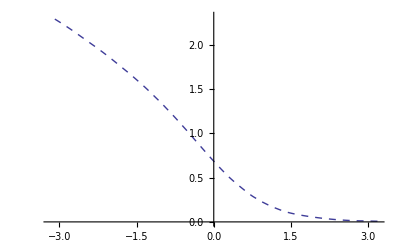

```mathematica
dtPlot=ListLinePlot[Transpose[{intact,dtL}],InterpolationOrder->2,PlotStyle->Dashed]
```

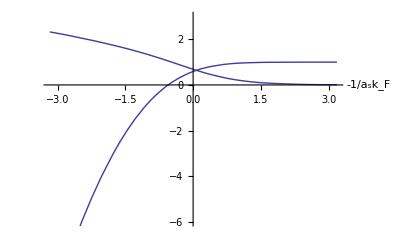

```mathematica
Show[dtPlot,muPlot,AxesLabel->{"-1/a_sk_F",""},AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->{-6,3}]
```

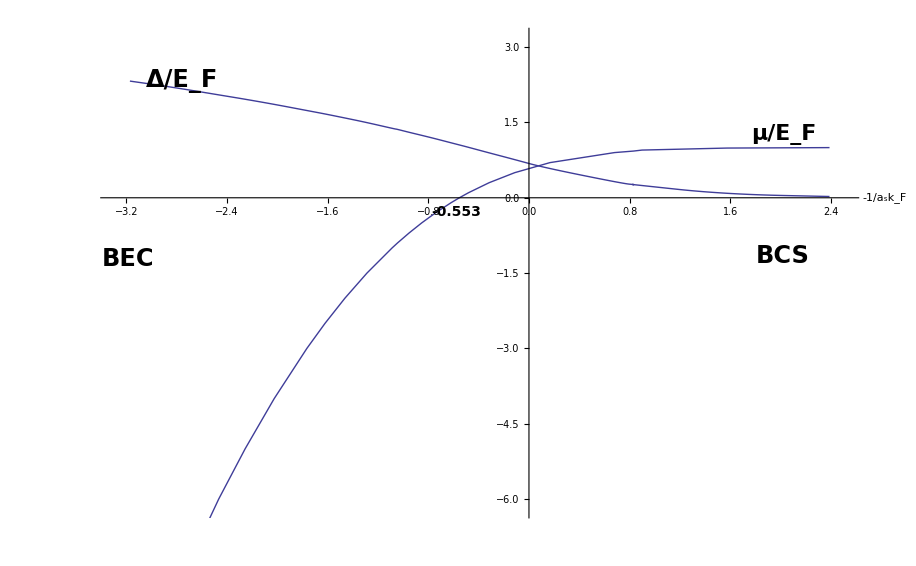

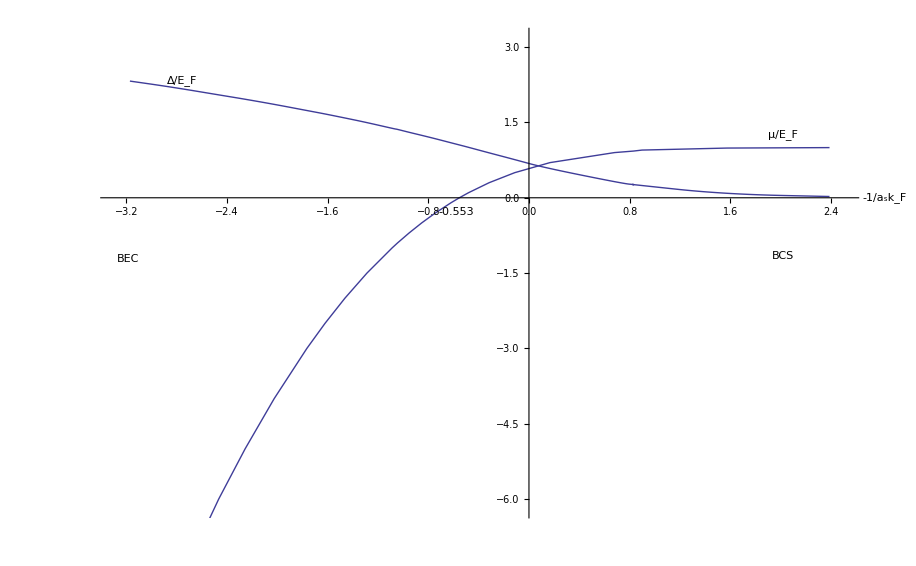

```mathematica
alpha2=3*2^(1/2)*dtL^2/(128*(dtt *2)^(1/2))
```

{(1.25001×10^-6)/(√dtt),0.000015/(√dtt),0.000186715/(√dtt),0.000632126/(√dtt),0.00111671/(√dtt),0.00136817/(√dtt),0.00162422/(√dtt),0.00241359/(√dtt),0.00516797/(√dtt),0.00796875/(√dtt),0.0107824/(√dtt),0.0135234/(√dtt),0.0187617/(√dtt),0.0236719/(√dtt),0.0259453/(√dtt),0.028125/(√dtt),0.0323438/(√dtt),0.0362109/(√dtt),0.0398438/(√dtt),0.0434531/(√dtt),0.0448828/(√dtt),0.0525/(√dtt),0.0591797/(√dtt),0.0652734/(√dtt),0.0707813/(√dtt),0.0810938/(√dtt),0.0902344/(√dtt),0.0984375/(√dtt),0.113672/(√dtt),0.126563/(√dtt)}

```mathematica
weight=1/(1+alpha2)^(2/3);shiftIntact=intact*(weight)^(1/2)+muL*2;intactShift=(shiftIntact*weight^(1/2));intactShift=((intact*weight^(1/2))+2muL*(weight))*weight^(-1/2);
```

```mathematica
intactSt2=intact*(2*30)^(1/2)+muL*2
```

{26.649,20.5087,14.1845,10.9763,9.39053,8.80266,8.29463,7.07284,4.44627,2.69077,1.29917,0.122885,-1.85401,-3.52722,-4.28534,-5.00472,-6.35361,-7.60327,-8.7784,-9.89641,-10.4326,-12.9787,-15.3359,-17.5585,-19.6784,-23.6916,-27.4816,-31.1084,-38.0109,-44.5765}

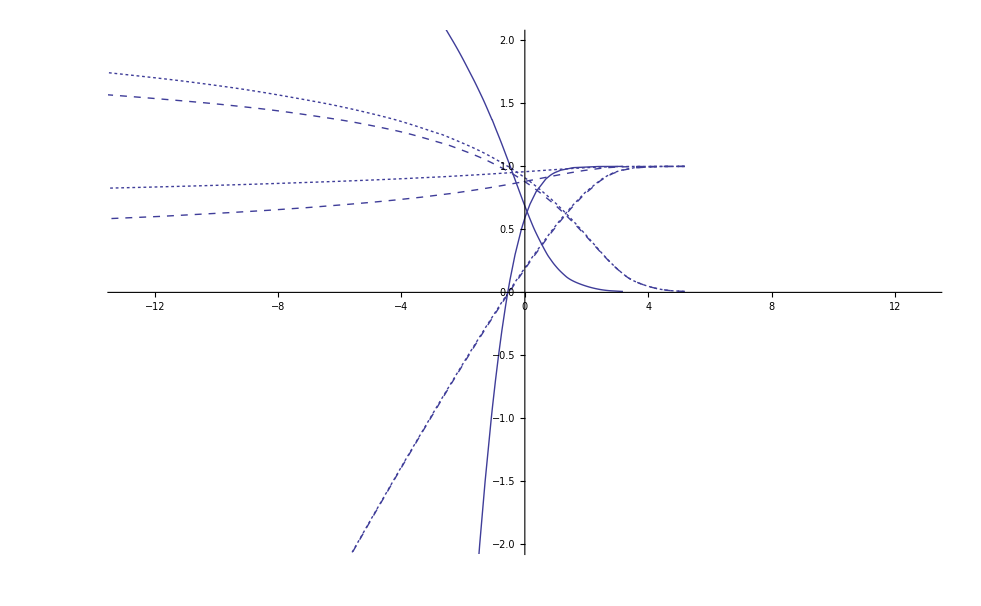

```mathematica
muPlotSt=ListLinePlot[Transpose[{intactShift,muL*weight}]/.{dtt->0.01},PlotStyle->{Dashed}];
wPlot=ListLinePlot[Transpose[{intactShift,weight}]/.{dtt->.01},PlotStyle->{Dashed}];
dtPlotSt=ListLinePlot[Transpose[{intactShift,dtL*weight}]/.{dtt->.03},InterpolationOrder->2,PlotStyle->{Dashed}];
muPlotSt2=ListLinePlot[Transpose[{intactShift, muL*weight}]/.{dtt->0.1},PlotStyle->{Dashing[Tiny]}];dtPlotSt2=ListLinePlot[Transpose[{intactShift,dtL*weight}]/.{dtt->0.1},InterpolationOrder->2,PlotStyle->{Dashing[Tiny]}];
wPlotSt2=ListLinePlot[Transpose[{intactShift,weight}]/.{dtt->.1},PlotStyle->{Dashing[Tiny]}];
Show[dtPlotSt,muPlotSt,dtPlot,wPlot,muPlot,muPlotSt2,dtPlotSt2,wPlotSt2,AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->{{-13,13},{-2,2}}]
```

```mathematica
ListLinePlot[Transpose[{intactShift, muL*weight}]/.{dtt->0.1.08}]
```

-Graphics-

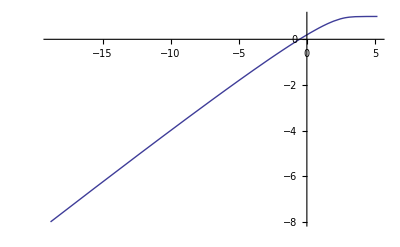

```mathematica
ListLinePlot[Transpose[{intactShift,muL*weight}]/.{dtt->0.1}]
```

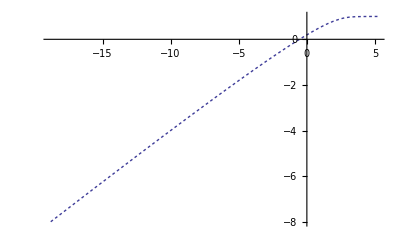

```mathematica
ListLinePlot[Transpose[{intactShift, muL*weight}]/.{dtt->0.1},PlotStyle->{Dashing[Tiny]}]
```

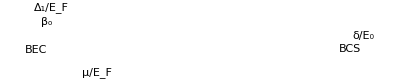
```mathematica
symbol=-Graphics-;
```

```mathematica
muPlotSt3=ListLinePlot[Transpose[{intactShift,muL*weight}]/.{dtt->0.001},InterpolationOrder->3];
muPlotSt4=ListLinePlot[Transpose[{intactShift*weight^(-1/2),muL*weight}]/.{dtt->0.001},InterpolationOrder->3];
wPlot3=ListLinePlot[Transpose[{intactShift,weight^(3/2)}]/.{dtt->.001},InterpolationOrder->5];
dtPlotSt3=ListLinePlot[Transpose[{intactShift,dtL*weight}]/.{dtt->.001}];Show[dtPlotSt3,muPlotSt3,wPlot3,muPlot,dtPlot,AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->{{-8,4},{-1.5,1.1}}]
```

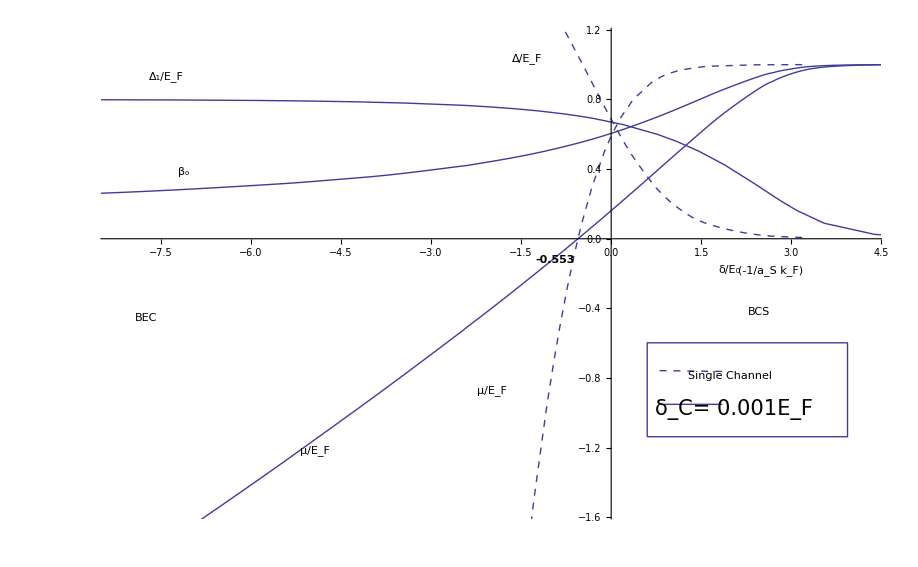
```mathematica
narrowPlotNew001=-Graphics-;
```

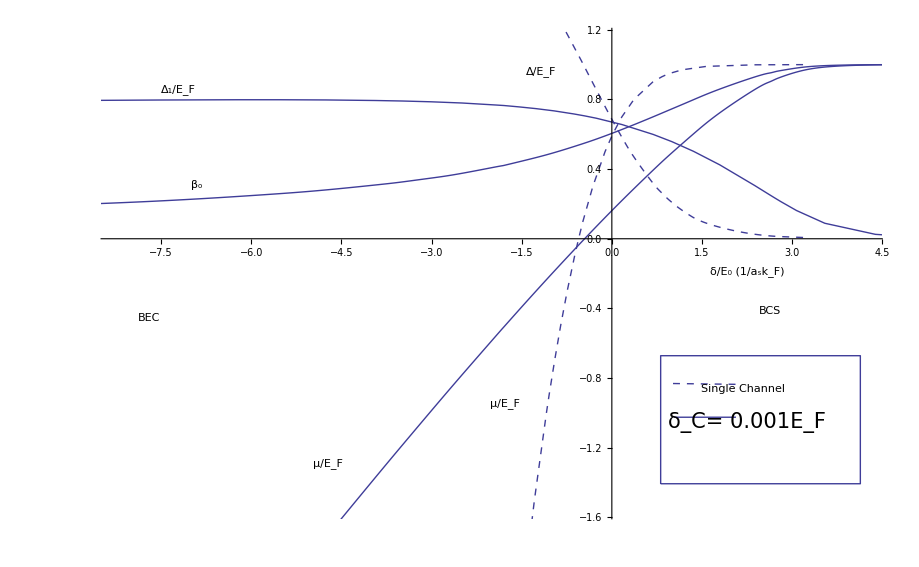

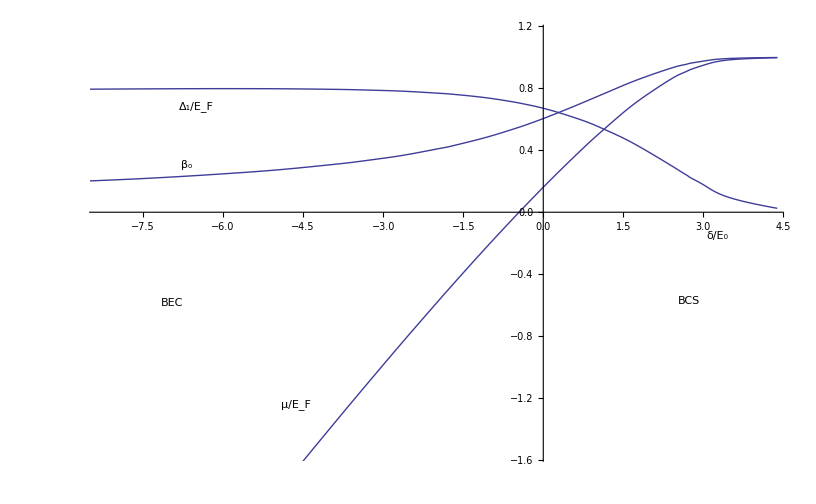
```mathematica
narrowPlot001=-Graphics-;
```

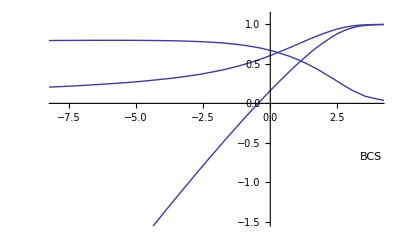

```mathematica
Show[dtPlotSt3,muPlotSt3,wPlot3,symbol,AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->{{-8,4},{-1.5,1.1}}]
```

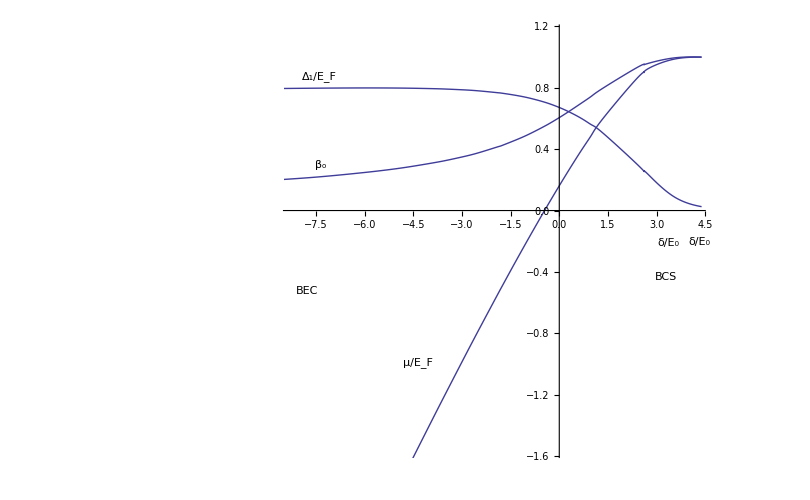
```mathematica
narrow001=-Graphics-;
```

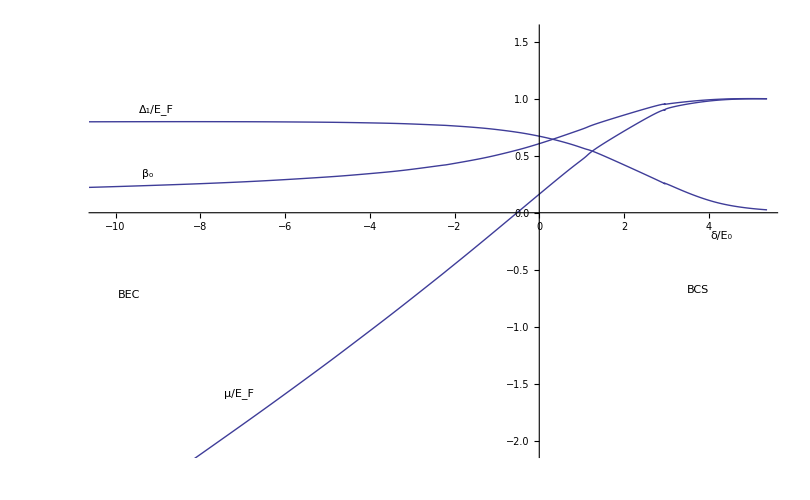

-Graphics-

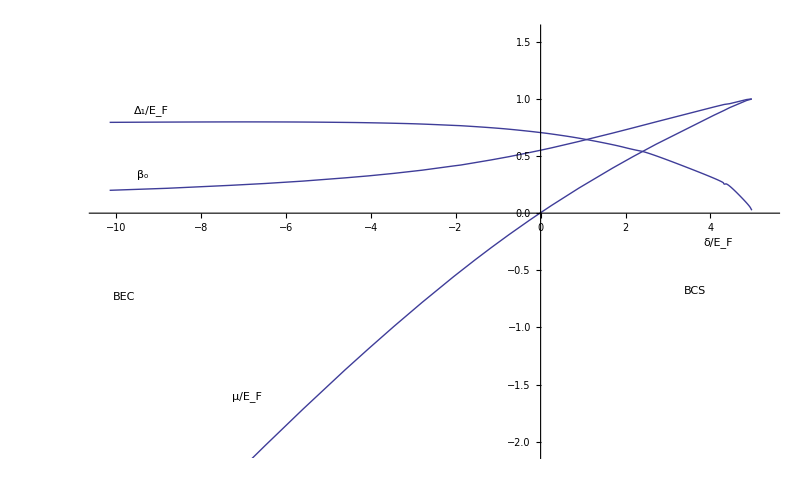

-Graphics-

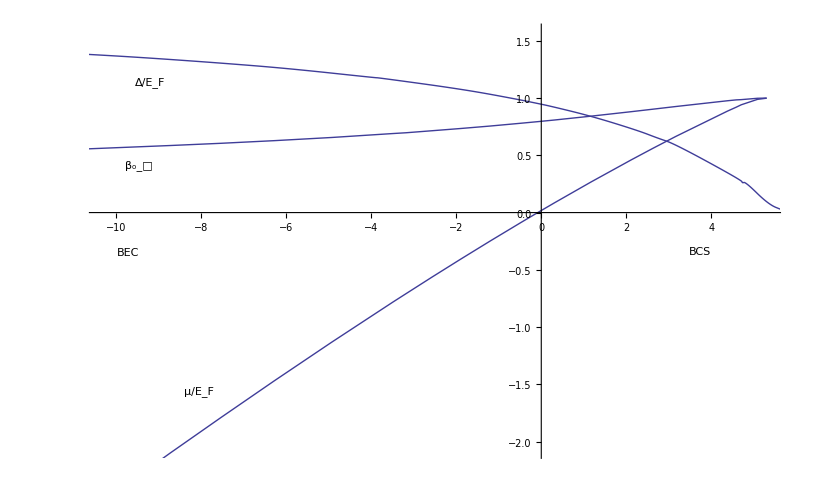

-Graphics-

-Graphics-

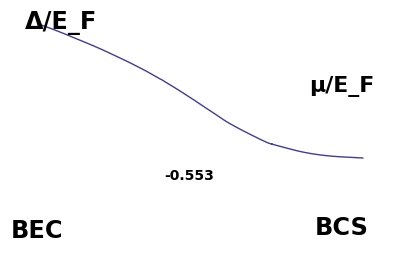
```mathematica
s=-Graphics-
```

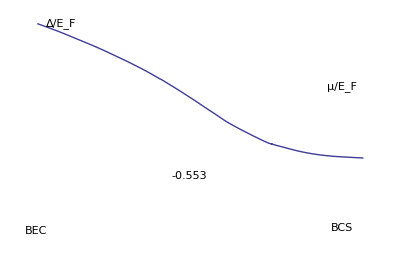

```mathematica
muDtL[[1]]
```

{0.9999,0.0000533339}

```mathematica
Length[muDtL]
```

30

```mathematica
a=0;a=
```

ListLinePlot::ioproc: {{1.9998  + 3.1822/(1 + 1.25001×10^-6\ Power[« 2 »])^1/3, 0.007303}, {1.998  + 2.38973/(1 + 0.000015\ Power[« 2 »])^1/3, 0.0252982}, {1.98  + 1.5756/(1 + 0.000186715\ Power[« 2 »])^1/3, 0.0892553}, « 24 », {-12 - 2.46689/(1 + 0.0984375\ Power[« 2 »])^1/3, 2.04939}, {-16 - 2.84159/(1 + 0.113672\ Power[« 2 »])^1/3, 2.20227}, {-20 - 3.17282/(1 + 0.126563\ Power[« 2 »])^1/3, 2.32379}}
 may contain non-machine precision numbers, complex numbers, or invalid entries.

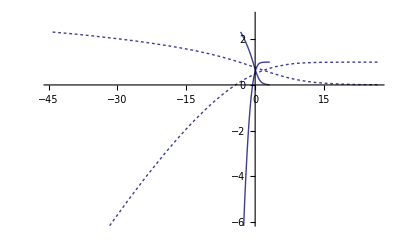

```mathematica
muPlotSt=ListLinePlot[Transpose[{shiftIntact, muL}],PlotStyle->{Dashed}];dtPlotSt=ListLinePlot[Transpose[{shiftIntact,dtL}],InterpolationOrder->2,PlotStyle->{Dashed}];
muPlotSt2=ListLinePlot[Transpose[{intactSt2, muL}],PlotStyle->{Dashing[Tiny]}];dtPlotSt2=ListLinePlot[Transpose[{intactSt2,dtL}],InterpolationOrder->2,PlotStyle->{Dashing[Tiny]}];
Show[dtPlotSt,muPlotSt,dtPlot,muPlot,muPlotSt2,dtPlotSt2,AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->{-6,3}]
```

```mathematica
Transpose[{intactShift,weight}]/.{dtt->0.1}
```

{{5.18199,0.999997},{4.38763,0.999968},{3.55451,0.999607},{3.10322,0.99867},{2.86143,0.997653},{2.76702,0.997126},{2.68295,0.99659},{2.4699,0.994944},{1.94827,0.989251},{1.54222,0.983545},{1.18613,0.977896},{0.860804,0.972469},{0.2666,0.962305},{-0.279139,0.953015},{-0.538883,0.948789},{-0.791873,0.944781},{-1.28135,0.937142},{-1.7525,0.930274},{-2.20911,0.923936},{-2.65327,0.917744},{-2.87217,0.915321},{-3.93196,0.902671},{-4.94984,0.891931},{-5.93503,0.882408},{-6.89499,0.874016},{-8.74796,0.858826},{-10.5347,0.845902},{-12.2703,0.834709},{-15.603,0.814871},{-18.8156,0.798978}}

```mathematica
weight/.{dtt->0.001}
```

{0.999974,0.999684,0.996083,0.986892,0.977129,0.972158,0.96716,0.952148,0.904012,0.860859,0.822345,0.788713,0.733053,0.688987,0.670726,0.654313,0.625218,0.601224,0.580673,0.561909,0.554887,0.520864,0.494996,0.474019,0.456866,0.428557,0.406848,0.389556,0.361826,0.341892}

```mathematica
weight
```

{1/((1+(1.25001×10^-6)/(√dtt))^(2/3)),1/(1+0.000015/(√dtt))^(2/3),1/(1+0.000186715/(√dtt))^(2/3),1/(1+0.000632126/(√dtt))^(2/3),1/(1+0.00111671/(√dtt))^(2/3),1/(1+0.00136817/(√dtt))^(2/3),1/(1+0.00162422/(√dtt))^(2/3),1/(1+0.00241359/(√dtt))^(2/3),1/(1+0.00516797/(√dtt))^(2/3),1/(1+0.00796875/(√dtt))^(2/3),1/(1+0.0107824/(√dtt))^(2/3),1/(1+0.0135234/(√dtt))^(2/3),1/(1+0.0187617/(√dtt))^(2/3),1/(1+0.0236719/(√dtt))^(2/3),1/(1+0.0259453/(√dtt))^(2/3),1/(1+0.028125/(√dtt))^(2/3),1/(1+0.0323438/(√dtt))^(2/3),1/(1+0.0362109/(√dtt))^(2/3),1/(1+0.0398438/(√dtt))^(2/3),1/(1+0.0434531/(√dtt))^(2/3),1/(1+0.0448828/(√dtt))^(2/3),1/(1+0.0525/(√dtt))^(2/3),1/(1+0.0591797/(√dtt))^(2/3),1/(1+0.0652734/(√dtt))^(2/3),1/(1+0.0707813/(√dtt))^(2/3),1/(1+0.0810938/(√dtt))^(2/3),1/(1+0.0902344/(√dtt))^(2/3),1/(1+0.0984375/(√dtt))^(2/3),1/(1+0.113672/(√dtt))^(2/3),1/(1+0.126563/(√dtt))^(2/3)}

```mathematica
alpha2/.{dtt->0.01}
```

{0.0000125001,0.00015,0.00186715,0.00632126,0.0111671,0.0136817,0.0162422,0.0241359,0.0516797,0.0796875,0.107824,0.135234,0.187617,0.236719,0.259453,0.28125,0.323438,0.362109,0.398438,0.434531,0.448828,0.525,0.591797,0.652734,0.707813,0.810938,0.902344,0.984375,1.13672,1.26563}

```mathematica
alpha2
```

{(1.25001×10^-6)/(√dtt),0.000015/(√dtt),0.000186715/(√dtt),0.000632126/(√dtt),0.00111671/(√dtt),0.00136817/(√dtt),0.00162422/(√dtt),0.00241359/(√dtt),0.00516797/(√dtt),0.00796875/(√dtt),0.0107824/(√dtt),0.0135234/(√dtt),0.0187617/(√dtt),0.0236719/(√dtt),0.0259453/(√dtt),0.028125/(√dtt),0.0323438/(√dtt),0.0362109/(√dtt),0.0398438/(√dtt),0.0434531/(√dtt),0.0448828/(√dtt),0.0525/(√dtt),0.0591797/(√dtt),0.0652734/(√dtt),0.0707813/(√dtt),0.0810938/(√dtt),0.0902344/(√dtt),0.0984375/(√dtt),0.113672/(√dtt),0.126563/(√dtt)}

```mathematica
dtL
```

{0.007303,0.0252982,0.0892553,0.164228,0.21828,0.241609,0.263249,0.320905,0.469574,0.583095,0.67827,0.759605,0.894707,1.00499,1.05214,1.09545,1.17473,1.24298,1.30384,1.36162,1.38384,1.49666,1.58902,1.66883,1.73781,1.86011,1.96214,2.04939,2.20227,2.32379}

```mathematica
dtL*weight/.{dtt->.001}
```

{0.00730281,0.0252902,0.0889056,0.162075,0.213288,0.234882,0.254604,0.305549,0.424501,0.501963,0.557772,0.599111,0.655867,0.692424,0.705699,0.716764,0.734465,0.74731,0.757105,0.765105,0.767872,0.779558,0.786561,0.791058,0.793948,0.797162,0.798294,0.798353,0.79684,0.794486}

```mathematica
Transpose[{intactShift,dtL*weight}]/.{dtt->.001}
```

{{5.1819,0.00730281},{4.38672,0.0252902},{3.54475,0.0889056},{3.07347,0.162075},{2.81245,0.213288},{2.70884,0.234882},{2.61587,0.254604},{2.3781,0.305549},{1.79579,0.424501},{1.35981,0.501963},{0.998423,0.557772},{0.68815,0.599111},{0.168583,0.655867},{-0.261609,0.692424},{-0.453088,0.705699},{-0.63261,0.716764},{-0.962459,0.734465},{-1.26222,0.74731},{-1.5388,0.757105},{-1.79496,0.765105},{-1.92071,0.767872},{-2.49233,0.779558},{-3.00961,0.786561},{-3.48634,0.791058},{-3.93478,0.793948},{-4.75461,0.797162},{-5.50802,0.798294},{-6.21437,0.798353},{-7.4985,0.79684},{-8.69304,0.794486}}